```mathematica
accuracy = 10^-6;
functionToCalc[x_] = E^x-3;
```

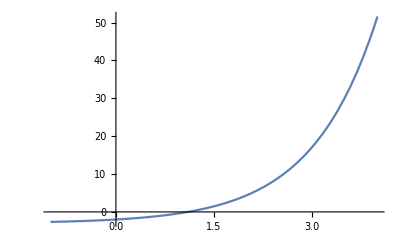

```mathematica
experimentPlot = Plot[functionToCalc[x], {x, -1,4}]
```

```mathematica
intervalStart = 0;
intervalEnd =2;
itterationCounter =0;
```

```mathematica
While[intervalEnd - intervalStart > accuracy,
currentResult =   functionToCalc[intervalStart]*functionToCalc[(intervalStart+intervalEnd)/2];
If[currentResult < 0, intervalEnd = (intervalStart+intervalEnd)/2, intervalStart = (intervalStart+intervalEnd)/2];
]
intervalEnd//N
currentResult //N
```

1.09861

-2.04282×10^-12